```mathematica
SetDirectory[NotebookDirectory[]];
sp0=Import["sp2.txt","Table"];
n0 = (Length@sp0+1)/3;
cx=sp0⟦1;;n0⟧;
cy=sp0⟦n0+1;;n0*2⟧;
h=sp0⟦2 n0+1;;-1⟧;
(*Length@data*)
Subscript[sx, i_][t_?NumberQ]:=cx⟦i,1⟧+cx⟦i,2⟧t+(cx⟦i,3⟧t^2+cx⟦i,4⟧t^3+cx⟦i,5⟧t^4+cx⟦i,6⟧t^5)
Subscript[sy, i_][t_?NumberQ]:=cy⟦i,1⟧+cy⟦i,2⟧t+(cy⟦i,3⟧t^2+cy⟦i,4⟧t^3+cy⟦i,5⟧t^4+cy⟦i,6⟧t^5)
{x[t_],y[t_]}=50(1+0.05Cos[8t-π]){Sin[t],Cos[t]};
(*Table[{Subscript[sx, i][t],Subscript[sy, i][t]},{i,1,Length@cx-1}];
Show[
ListPlot[Transpose[{cx⟦1;;-1,1⟧,cy⟦1;;-1,1⟧}]]
,ParametricPlot[{%⟦1;;n0-1;;2⟧,%⟦2;;n0-1;;2⟧},{t,0,1},AspectRatio->Automatic,PlotStyle->{Blue,Red}]
,AspectRatio->Automatic,ImageSize->Medium]*)
```

0

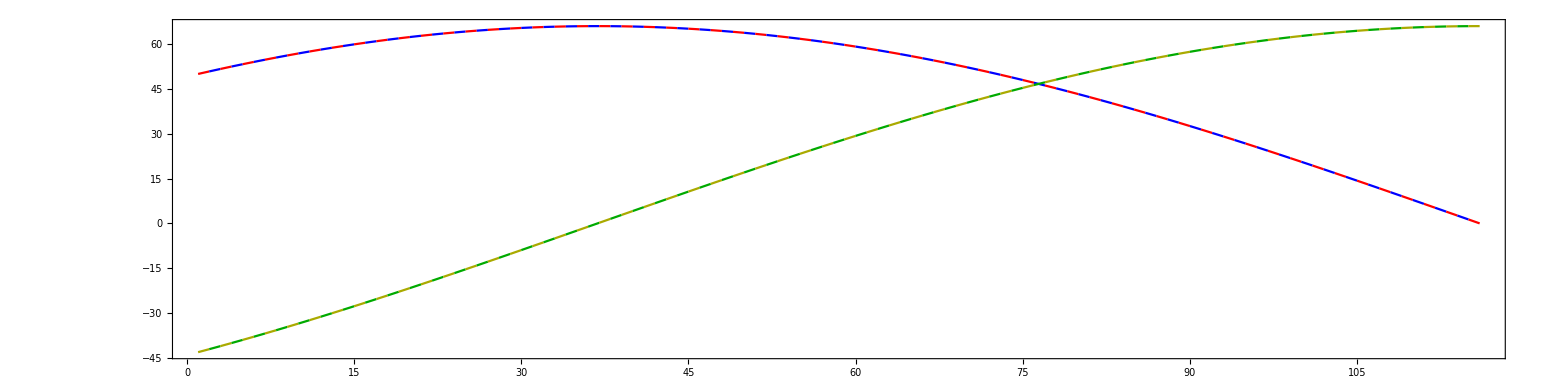

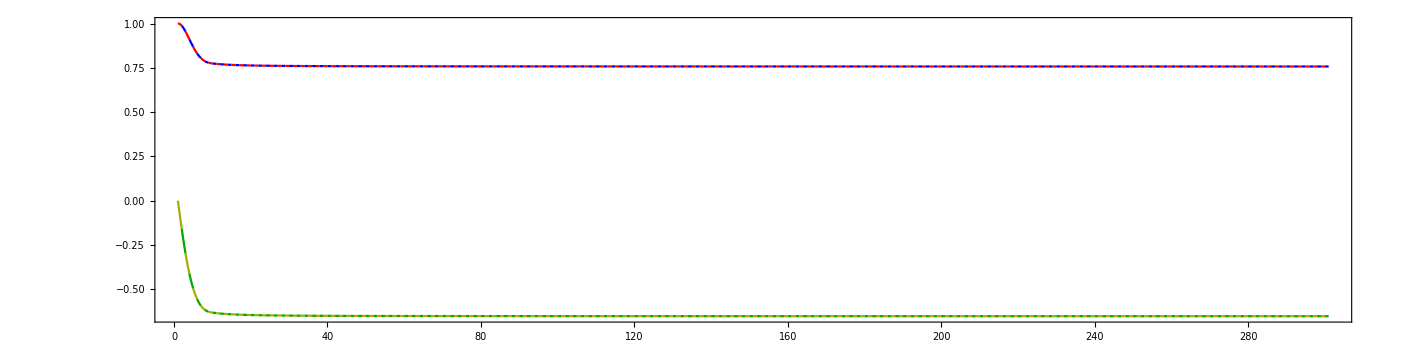

```mathematica
dv=0
tx = Table[Flatten@{#+i,Derivative[dv][Subscript[sx, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.1],{i,Range[1,n0-1]}];
ty = Table[Flatten@{#+i,Derivative[dv][Subscript[sy, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.1],{i,Range[1,n0-1]}];
(*ty = Table[{t+i,Derivative[dv][Subscript[sy, i]][t]/h⟦i⟧^dv},{i,1,Length@cx-1}];*)
Show[
ListPlot[tx,PlotStyle->{Red,Blue},Joined->True,PlotRange->All],
ListPlot[ty,PlotStyle->Darker@{Yellow,Green},Joined->True,PlotRange->All],
Axes->True,
(*ParametricPlot[{ty⟦1⟧,ty⟦2⟧},{t,0,1}],*)
AspectRatio->0.25,Frame->True,PlotRange->All]
```

{0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997,0.0302997}

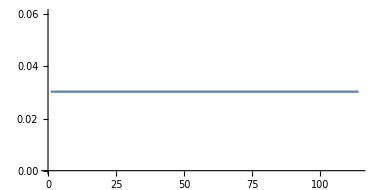

```mathematica
Clear[i,kv,kvt]
θ=Table[ArcCos[Subscript[sy, i][0]/√((Subscript[sx, i][0])^2+ (Subscript[sy, i][0])^2)],{i,1,Length@cx}];//Quiet;
Subscript[kv, i_][t_]:=(Subscript[sx, i]'[t]Subscript[sy, i]''[t]-Subscript[sy, i]'[t]Subscript[sx, i]''[t])/((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)^1.5+(Subscript[sy, i]'[t])/Subscript[sx, i][t]/√((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)
kvt[t_]:=(x'[t]y''[t]-y'[t]x''[t])/(x'[t]^2+y'[t]^2)^1.5
Table[Subscript[kv, i][0.],{i,2,n0-1 }]
Show[ListPlot[%,PlotRange->All,Joined->True],AspectRatio->0.5]
```